# Лабораторная работа 8. Локальные преобразования и графика.

Выполнила студентка ММФ БГУ
 1 к, 5 гр. Шклярик В.С.
 27 октября 2021

## Задание 1. Правила локальных преобразований при построении графических объектов.

```mathematica
Fig1=Graphics3D[{AbsoluteThickness[3],Line[{{0,0,0},{1,0,0}}]},Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
ab={{0,0,0},{1,0,0}};V={0,1,0};(#+V)&/@ab
```

{{0,1,0},{1,1,0}}

```mathematica
Fig2=Graphics3D[{{AbsoluteThickness[3],Hue[0],Line[ab]},{AbsoluteThickness[3],Hue[.5],Line[(#+V)&/@ab]}},Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
Line[P_]:>{Line[P],Line[#+V&/@P]};
```

```mathematica
Fig1/.Line[P_]:>{Line[P],Hue[0.3],Line[#+{0,1,0}&/@P]}//FullForm
```

Graphics3D[List[AbsoluteThickness[3],List[Line[List[List[0,0,0],List[1,0,0]]],Hue[0.3],Line[List[List[0,1,0],List[1,1,0]]]]],Rule[Axes,True],Rule[AxesLabel,List["X","Y","Z"]]]

```mathematica
Fig2=Show[Fig1/.Line[P_]:>{Line[P],Hue[.5],Line[#+{0,1,0}&/@P]},Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
ab={{0,0,0},{1,0,0}};V={0,1,0};{#,#+V}&/@ab
```

{{{0,0,0},{0,1,0}},{{1,0,0},{1,1,0}}}

```mathematica
Fig2=Show[Fig1/.Line[P_]:>{Line[P],Line[#+V&/@P],Hue[.5],Line[{#,#+V}]&/@P},Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Fig3=Show[Fig2/.Line[P_]:>{Line[P],Line[#+{0,0,1}&/@P],Hue[1/3],Line[{#,#+{0,0,1}}]&/@P},Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Shift[Fig_,Vector_,Color_]:=Fig/.Line[P_]:>{Line[P],Line[#+Vector&/@P],Color,Line[{#,#+Vector}]&/@P}
```

```mathematica
Show[Fig4=Shift[Fig3,{1.5,1,1},Hue[12]]]
```

-Graphics3D-

```mathematica
Show[Fig5=Shift[Fig4,{-1.5,1,1},Hue[1/6]]]
```

-Graphics3D-

## Задание 2. Построение геометрических фракталов

Напишите функцию fracLine[{A:{_,_},B:{_,_}}], генерирующую из произвольного отрезка AB указанный фрактальный фрагмент, согласно варианту.

```mathematica
ClearAll[fracLine2]
```

```mathematica
base = {{0,0},{1/2,1/2},{1,0}};(*основа фрактала*)
```

```mathematica
fracLine2[  fracLine[A_,B_]  ]:=Module[{x,y,fragment},{x,y}=B-A; fragment=  ( A+ {{x,-y},{y,x}}. # & )/@base;Map[ fracLine@@# & ,Partition[ fragment,2,1]] ]
fracLine2[fracLine_]:=fracLine2/@fracLine;
```

```mathematica
fracLine2[fracLine[{0,0},{1,0}]]
```

{fracLine[{0,0},{1/2,1/2}],fracLine[{1/2,1/2},{1,0}]}

```mathematica
fracLine2[fracLine[{0,0},{1/2,1/2}]]
```

{fracLine[{0,0},{0,1/2}],fracLine[{0,1/2},{1/2,1/2}]}

```mathematica
fracShow[n_Integer?Positive,fL_] :=Show[Graphics[Nest[fracLine2,fL,n]/.fracLine[x__]->Line[{x}]],AspectRatio->Automatic]
```

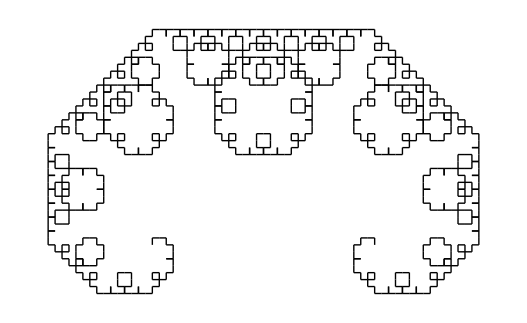

```mathematica
fracShow[10,fracLine[{0,0},{1,0}]]
```

## Задание 4. Закрепление навыков и умений

Nest- обеспечивает последовательное применение функции к результату применения функции к выражению заданное число раз, Partition- выделяет из списка подсписки заданной длины с заданным “шагом” , Module-функция, локализующая имена переменных(задающая им новые имена), RuleDelayed- правило, оставляющее значения правой части невычисленными до момента вызова.